### FCM Lib Import

```mathematica
SetDirectory@NotebookDirectory[]
Needs["FCMLib`",FileNameJoin[{NotebookDirectory[],"../lib/","FCMLib-cur.wl"}]]
$FCMLibVersion
$activationThreshold
```

/Users/oosoba/Documents/RAND/Coding/fcm-fusion/socsim

Fuzzy Cognitive Map Library ver. 0.0.8

0.5

### Thucydides Trap Dev

#### Preamble

```mathematica
logisticActvn[t_]:=Max[0,LogisticSigmoid[7.5t-3.5]];
SetAttributes[logisticActvn,{Listable,NumericFunction}]

linearActvn[t_]:=Min[Max[0,t],1];
SetAttributes[linearActvn,{Listable,NumericFunction}]


(* LU Activation: *)
{$activationFxn, $activationBias} = {linearActvn, 0};
```

```mathematica
trapvs=Import["./trap-verts.csv", "CSV"];
trapvs⟦;;,2;;⟧=StringTrim/@trapvs⟦;;,2;;⟧; 
n =Length@trapvs
```

17

```mathematica
addjitter=0.075;
strongOrLink=$activationThreshold/2 ;
orLink=strongOrLink(*-0.05*);
weakOrLink=$activationThreshold/4;
unsure=orLink;
andLink=$activationThreshold/3;
subAndLink=$activationThreshold + 2×addjitter;
```

#### Static Specification

```mathematica
(statictrapspec={
{2,1,subAndLink},{3,1,subAndLink},
{1,2,subAndLink},{1,3,subAndLink},
{4,1,-weakOrLink},(*FEAR edges*)

{5,6,subAndLink},{6,5,subAndLink},
{5,7,subAndLink},{7,5,subAndLink},
{8,5,-weakOrLink},(*Honor edges*)

{14,12,-weakOrLink},{14,13,-weakOrLink},
{12,11,subAndLink},{13,11,subAndLink},
{15,11,weakOrLink+addjitter},(*Interests edges*)

{17,17,orLink},(*WAR self-excitations for temporal correlation/momentum of war*)
{1,17,1/3},{5,17,1/3},{11,17,1/3},(*TLD'and' links*)

{4,17,-andLink-addjitter},{9,17,-andLink-addjitter},{10,17,-andLink},{15,17,andLink}, (*Aux TLD'and' links*)
{16,17,andLink} (*Shi link...?*)
};)
```

```mathematica
(*Trivalent Quantization*)
statictrapspec⟦;;,3⟧ = (statictrapspec⟦;;,3⟧/.{x_/;x>0->1, x_/;x<0->-1});
(* Round[statictrapspec⟦;;,3⟧] 
{statictrapspec⟦;;,3⟧,
Round[statictrapspec⟦;;,3⟧],
statictrapspec⟦;;,3⟧/.{x_/;x>0->1, x_/;x<0->-1}
}//Transpose//TableForm

*)
```

```mathematica
strapFCM =FCM[trapvs,statictrapspec, 0.37];
```

### Illustrations

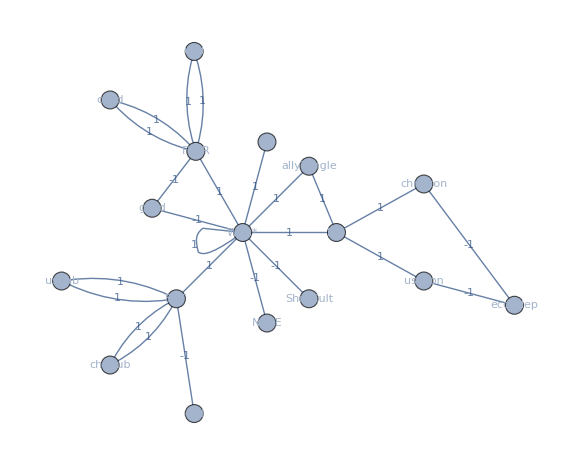
| Label | Full Description
1 | FEAR | Fear
2 | usd | US Military/Defense Posture
3 | chnd | China Military/Defense Posture
4 | geod | Geographical Distance
5 | ENT | Sense of Entitlement/Honor
6 | uspub | US Public Resentment
7 | chnpub | Chinese Public Resentment
8 | dipl | Diplomacy Channels & International Rules
9 | NUKE | Nuclear Power/MAD
10 | ShrdCult | Shared Culture
11 | INT | National Interests Clash
12 | usecon | US Economic Dominance
13 | chnecon | China Economic Dominance
14 | econdep | Economic Interdependence
15 | allyTangle | Alliance Network Structural Friction
16 | shi | Contextual/Historical Military Momentum
17 | WAR* | War-Graphics-

```mathematica
Row@{
TableForm[
trapvs⟦;;,{1,2,3}⟧,
TableHeadings->{None,Style[#,Bold]&/@{"", "Label","Full Description"}}
],
Graph[strapFCM,
GraphLayout->"RadialEmbedding",
ImageSize->72×8
]
}
```

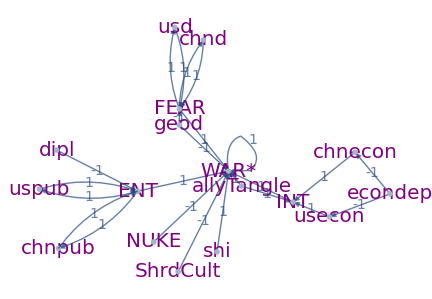

```mathematica
dtrapfig=Graph[
strapFCM,
GraphLayout->"SpringEmbedding",(* RadialEmbedding SpringElectricalEmbedding*)
EdgeLabelStyle-> Directive[14],
EdgeStyle->Thick,
EdgeShapeFunction->GraphElementData[{"HalfFilledArrow","ArrowSize"->0.04}],
VertexLabels->PropertyValue[strapFCM, VertexLabels],
VertexLabelStyle->Directive[Purple,Italic,20],
VertexShape->Graphics[{EdgeForm[Thick],LightBlue,Disk[{0,0},0.5×{1.5,1}]}],
VertexSize->0.6,
ImageSize->72×6
]
```

```mathematica
(*Export["dyn-ttrap-fcm.png",dtrapfig]*)
```

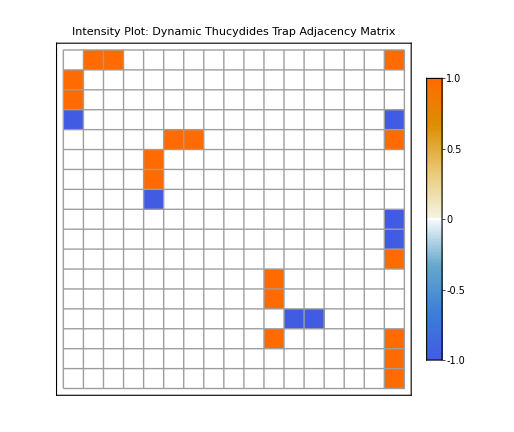

```mathematica
dtrapmtx=MatrixPlot[
FCMat@strapFCM, 
ImageSize->6×72,
ImageMargins->0,Mesh->All,
Frame->True,
FrameTicks->{None,None},
PlotLegends->Automatic,
PlotLabel->Style["Intensity Plot: Dynamic Thucydides Trap Adjacency Matrix", 32, Bold]
]
```

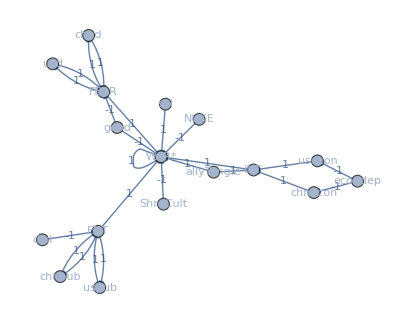

```mathematica
strapFCM
```

## Continuous Activation Exploration

```mathematica
fcms = {strapFCM};
```

#### Engineered Masks + Vertex Leverage Analysis

```mathematica
evcnt=Round[EigenvectorCentrality@strapFCM, 0.001];
bwcnt = Round[(#/Total[#])&@BetweennessCentrality@strapFCM, 0.001];
clcnt = Round[(#/Total[#])&@ClosenessCentrality@strapFCM, 0.001];

Row@{
TableForm[
Transpose[Transpose[trapvs⟦;;,{1,2,3}⟧]~Join~{evcnt,bwcnt, clcnt}],
TableHeadings->{None,Style[#,Bold]&/@{"", "Label","Full Description","Eig.", "Bwc.", "Close"}}
],
Graph[strapFCM,
GraphLayout->"SpringEmbedding",
ImageSize->72×6
]
}
```

```mathematica
(* 4:geod, 8:dipl, 
14:econdep - highest/equal closeness centrality,
15:allyTangle next up,
10:ShrdCult,  
*)
```

```mathematica
evcnt=Round[EigenvectorCentrality@strapFCM, 0.001];
bwcnt = Round[(#/Total[#])&@BetweennessCentrality@strapFCM, 0.001];
clcnt = Round[(#/Total[#])&@ClosenessCentrality@strapFCM, 0.001];

Row@{
TableForm[
Transpose[Transpose[trapvs⟦;;,{1,2,3}⟧]~Join~{evcnt,bwcnt, clcnt}],
TableHeadings->{None,Style[#,Bold]&/@{"", "Label","Full Description","Eig.", "Bwc.", "Close"}}
],
Graph[strapFCM,
GraphLayout->"RadialEmbedding",
ImageSize->72×6
]
}
```

#### Mask Engineering

```mathematica
(*logisticActvn[t_]:=Max[0,LogisticSigmoid[7.5t-3.5]];*)
logisticActvn[t_]:=Max[0,LogisticSigmoid[7.5t-2.5]];
SetAttributes[logisticActvn,{Listable,NumericFunction}]

linearActvn[t_]:=Min[Max[0,t],1];
SetAttributes[linearActvn,{Listable,NumericFunction}]
```

```mathematica
egmask0 = {
0,1,0,1,
0,1,0,1,
1,0,0,0,
1,1,0,0,
0
}; (* Nukes *)

egmask = {
0,1,0,1,
1,0,0,0,
0,1,0,0,
1,0,0,0,
0
}; (* Shared Culture + econ conflict *)

eg2mask = {
0,1,0,1,
1,0,0,1,
0,0,1,0,
1,0,0,0,
0
};  (* dipl intervene *)
eg3mask = {
0,1,0,1,
1,0,0,0,
-1,0,1,0,
1,1,0,0,
0
}; (* econ dep intervene, no nukes *)

eg4mask = {
0,1,0,1,
1,0,0,0,
1,1,1,0,
1,1,0,0,
0
}; (* econ dep intervene, with nukes *)

Grid[{
{TableForm@Transpose@{Pick[trapvs⟦;;,2⟧,egmask0,1],Pick[trapvs⟦;;,3⟧,egmask0,1]}},
{TableForm@Transpose@{Pick[trapvs⟦;;,2⟧,egmask,1],Pick[trapvs⟦;;,3⟧,egmask,1]}},
{TableForm@Transpose[{Pick[trapvs⟦;;,2⟧,eg2mask,1],Pick[trapvs⟦;;,3⟧,eg2mask,1]}],Style[TableForm@Transpose[{Pick[trapvs⟦;;,2⟧,eg2mask,-1],Pick[trapvs⟦;;,3⟧,eg2mask,-1]}], Red]},
{TableForm@Transpose[{Pick[trapvs⟦;;,2⟧,eg3mask,1],Pick[trapvs⟦;;,3⟧,eg3mask,1]}],
Style[TableForm@Transpose[{Pick[trapvs⟦;;,2⟧,eg3mask,-1],Pick[trapvs⟦;;,3⟧,eg3mask,-1]}], Red]}
},Frame->All]
```

```mathematica
(* Engineered example that leads diff model behavior *)
{Pick[trapvs⟦;;,2⟧,egmask,1], Pick[trapvs⟦;;,2⟧,egmask,-1]}
{Pick[trapvs⟦;;,2⟧,eg2mask,1], Pick[trapvs⟦;;,2⟧,eg2mask,-1]}
{Pick[trapvs⟦;;,2⟧,eg3mask,1], Pick[trapvs⟦;;,2⟧,eg3mask,-1]}
{Pick[trapvs⟦;;,2⟧,eg4mask,1], Pick[trapvs⟦;;,2⟧,eg4mask,-1]}
```

#### Comparisons

```mathematica
Manipulate[
fins=((FCMEvolSeq[#,inp,mask]&)/@fcms);
res=Transpose@{fcms, fins};
Panel[$activationFxn];
Row[{
TableForm[
Transpose[{inp, mask}~Join~Chop[SetAccuracy[fins⟦;;,-1,;;⟧,3],10^-2]],
TableHeadings->{
MapThread[Style[(#1<>#2<>#3), 14]&,{trapvs⟦;;,3⟧,ConstantArray["|", n],trapvs⟦;;,2⟧}],
{"inp", "mask","Dyn.", "Static"}
},
TableAlignments->Right, TableSpacing->{2,1.5}
],

TabView[
Table[
(FCMView[Graph[#1, GraphLayout->"RadialEmbedding", ImageSize->72×6], #2, trapvs]&)@@res⟦ev⟧,
{ev,Range@Length@res}
],1
],

GraphicsRow[
MatrixPlot[#, 
ColorRules->{x_/;0≤x≤0.45->LightBlue,x_/;0.45<x≤0.65->Orange,x_/;x≤0.65->White},
ImageSize->Large,
ImageMargins->0,
FrameTicks->{None,Automatic} ,
FrameTicksStyle->Directive[20, Bold]
]&/@(Transpose/@fins),
ImageMargins->0
]

},"|",
ImageSize->72×32
],

{{inp,egmask0(*ConstantArray[0,n]*)(*RandomInteger[{0,1},n]*)},ControlType->None},
{{mask,(*ConstantArray[0,n]*)egmask0 },ControlType->None},


Dynamic@Panel@Grid[{
{SetterBar[Dynamic[{$activationFxn, $activationBias}],{{linearActvn,0},{logisticActvn,0},{UnitStep,0.5}}], Text[{$activationFxn, $activationBias}]},
Outer[Text[Style[trapvs⟦#,2⟧, 14]]&,Range[n]],
Outer[Checkbox[Dynamic[inp⟦#⟧],{0,1}]&,Range[n]],
Outer[Checkbox[Dynamic[mask⟦#⟧],{0,1,-1}]&,Range[n]]
}, Alignment->Right
]
]
```

```mathematica
(* culture node mediates change from war to no war *) 
rule=x_?NumberQ/;0.5<Abs[x]<1.2:>{Style[x,Bold,Background->LightRed]};

TableForm[
Transpose[Chop[SetAccuracy[fins⟦1⟧,2],10^-1]]/.rule,
TableHeadings->{
MapThread[Style[(#1<>#2<>#3), 14]&,{trapvs⟦;;,3⟧,ConstantArray["|", n],trapvs⟦;;,2⟧}],
("t="<>ToString@#)&/@Range[(Dimensions@fins)⟦2⟧]
},
TableAlignments->Right, TableSpacing->Automatic(*{2,2.5}*)
](*/.rule*)
```

| t=1 | t=2 | t=3
Fear|FEAR | 0 | 0 | 0
US Military/Defense Posture|usd | 1. | 1. | 1.
China Military/Defense Posture|chnd | 0 | 0 | 0
Geographical Distance|geod | 1. | 1. | 1.
Sense of Entitlement/Honor|ENT | 0 | 0 | 0
US Public Resentment|uspub | 1. | 1. | 1.
Chinese Public Resentment|chnpub | 0 | 0 | 0
Diplomacy Channels & International Rules|dipl | 1. | 1. | 1.
Nuclear Power/MAD|NUKE | 1. | 1. | 1.
Shared Culture|ShrdCult | 0 | 0 | 0
National Interests Clash|INT | 0 | 1. | 1.
US Economic Dominance|usecon | 0 | 0 | 0
China Economic Dominance|chnecon | 1. | 1. | 1.
Economic Interdependence|econdep | 1. | 1. | 1.
Alliance Network Structural Friction|allyTangle | 0 | 0 | 0
Contextual/Historical Military Momentum|shi | 0 | 0 | 0
War|WAR* | 0 | 0 | 0

## Exhaustive Search & Analysis: Heaviside Activation Fxn

### Heaviside Activation Fxn

```mathematica
{$activationFxn, $activationBias} = {UnitStep,0.5}
stepres = Table[
{
(*IntegerDigits[inp, 2,n],*)
Last@Last@FCMEvolSeq[strapFCM,IntegerDigits[inp, 2,n],IntegerDigits[inp, 2,n]]
},
{inp,0, 2^n-1}
];
Export["qttrap-triv-step.csv", stepres];
```

{UnitStep,0.5}

```mathematica
stepres0 = stepres;
```

### Heaviside Activation Fxn

```mathematica
stepres =Flatten@ Import["qttrap-triv-step.csv"];
Dimensions@stepres
```

{131072}

```mathematica
trapvs
```

{{1,FEAR,Fear},{2,usd,US Military/Defense Posture},{3,chnd,China Military/Defense Posture},{4,geod,Geographical Distance},{5,ENT,Sense of Entitlement/Honor},{6,uspub,US Public Resentment},{7,chnpub,Chinese Public Resentment},{8,dipl,Diplomacy Channels & International Rules},{9,NUKE,Nuclear Power/MAD},{10,ShrdCult,Shared Culture},{11,INT,National Interests Clash},{12,usecon,US Economic Dominance},{13,chnecon,China Economic Dominance},{14,econdep,Economic Interdependence},{15,allyTangle,Alliance Network Structural Friction},{16,shi,Contextual/Historical Military Momentum},{17,WAR*,War}}

```mathematica
labels =trapvs⟦;;,2⟧
```

{FEAR,usd,chnd,geod,ENT,uspub,chnpub,dipl,NUKE,ShrdCult,INT,usecon,chnecon,econdep,allyTangle,shi,WAR*}

```mathematica
spaceSz = 2^n-1;
inpRange = Range[0,spaceSz];
validInpsB=Table[
IntegerDigits[inp, 2,n],
{inp,inpRange}
];
validIdx = Select[inpRange+1,(validInpsB⟦#,-1⟧≠1 )&];
Dimensions@validInpsB
validIdx//Length
```

{131072,17}

65536

{65536}

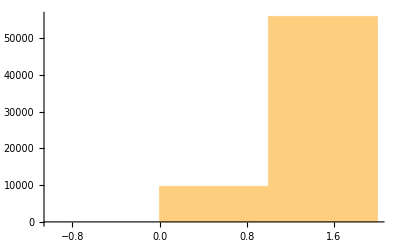

{1,1,1}

```mathematica
stepres = Flatten@stepres⟦validIdx⟧;
Dimensions@stepres
Histogram@stepres
Quartiles@stepres
```

#### War and Peace ...

```mathematica
nowars = Cases[
Range@Length@stepres,
i_/;stepres⟦i⟧==0
];(*//Length*)
Length@nowars
nwstates = (validInpsB⟦validIdx⟦#⟧⟧&/@nowars);

Print["Pct of Peace-vs-War Convergences:",100×Length[nowars]/(Length@stepres)//N]
```

9664

Pct of Peace-vs-War Convergences:14.7461

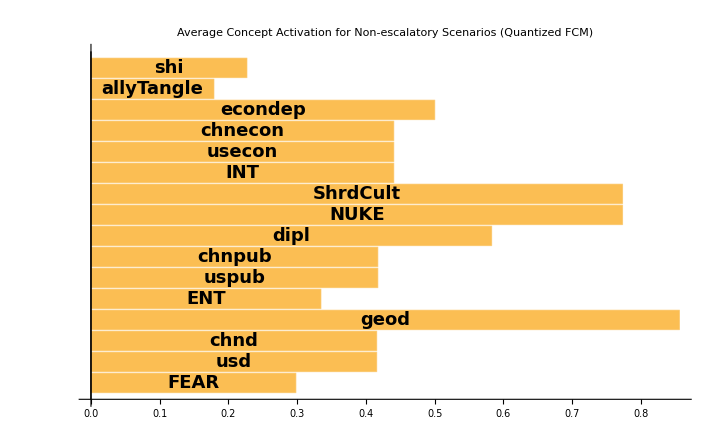

```mathematica
nwmeas = Mean@nwstates;
(*labels⟦Select[Range[n-1], (nwmeas⟦#⟧>0.45)&]⟧*)
BarChart[nwmeas⟦;;-2⟧,
ChartLabels->Placed[(Style[#, Bold, 18]&/@labels),Center],
BarOrigin->Left,
PlotLabel->Style["Average Concept Activation for Non-escalatory Scenarios\n(Quantized FCM)", Bold, 24],
PlotRange->All,
ImageSize->72×10
]
```

```mathematica
mTh=N@Mean@stepres;
wars = Cases[
Range@Length@stepres,
i_/;stepres⟦i⟧>mTh
];
wstates = (validInpsB⟦validIdx⟦#⟧⟧&/@wars);
```

```mathematica
wstates//Dimensions
```

{55872,17}

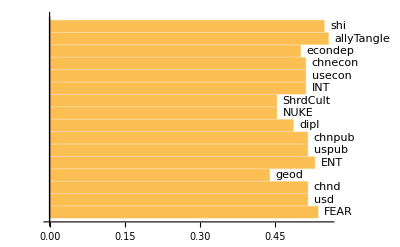

```mathematica
wmeas = Mean@wstates;
BarChart[wmeas⟦;;-2⟧,
ChartLabels->Placed[labels,After],
BarOrigin->Left,
 PlotRange->All]
```

## Exhaustive Search & Analysis: Other Activation Fxn

### Search: Linear Activation Fxn

```mathematica
{$activationFxn, $activationBias} = {linearActvn,0}

searchResults = Table[
{
(*IntegerDigits[inp, 2,n],*)
Last@Last@FCMEvolSeq[strapFCM,IntegerDigits[inp, 2,n],IntegerDigits[inp, 2,n]],
Last@Last@FCMEvolSeq[strapFCM,IntegerDigits[inp, 2,n],IntegerDigits[inp, 2,n]]
},
{inp,0, 2^n-1 (*300*)}
];
Export["dyn-stat-cmp-linear.csv", searchResults];

dWarStates = (Last/@searchResults);
sWarStates = (First/@searchResults);
Histogram/@{dWarStates,sWarStates}
Quartiles/@{dWarStates,sWarStates}
```

### Analysis: Linear Activation Fxn

```mathematica
linres = (Transpose@Import["dyn-stat-cmp-linear.csv"])⟦;;,validIdx⟧;
Dimensions@linres
Histogram/@linres
Quartiles/@linres
```

#### Dyn - Stat Divergence

```mathematica
divs = Cases[
Range@Length@linres⟦1⟧,
i_/;(Subtract@@(linres⟦;;,i⟧)≠0)
];
Length@divs
divmasks = (IntegerDigits[validIdx⟦#⟧, 2,n]&/@divs);
divmeas = Mean@divmasks;
BarChart[divmeas⟦;;-2⟧,
ChartLabels->Placed[labels,After],
BarOrigin->Left,
 PlotRange->All]
```

#### War and Peace ...

```mathematica
nowars = Cases[
Range@Length@linres⟦2⟧,
i_/;linres⟦2,i⟧≤0.5
];
nwstates = (IntegerDigits[validIdx⟦#⟧, 2,n]&/@nowars);

Print["Pct of Peace-vs-War Convergences:",100×Length[nowars]/(Length@linres⟦2⟧)//N]

nwmeas = Mean@nwstates;
(*labels⟦Select[Range[n-1], (nwmeas⟦#⟧>0.45)&]⟧*)
BarChart[nwmeas⟦;;-2⟧,
ChartLabels->Placed[(Style[#, Bold, 18]&/@labels),Center],
BarOrigin->Left,
PlotLabel->Style["Average Concept Activation for Non-escalatory Scenarios", Bold, 24],
PlotRange->All,
ImageSize->72×10
]
```

### Search: Logistic Activation Fxn

```mathematica
{$activationFxn, $activationBias} = {logisticActvn,0}

searchResults = Table[
{
(*IntegerDigits[inp, 2,n],*)
Last@Last@FCMEvolSeq[strapFCM,IntegerDigits[inp, 2,n],IntegerDigits[inp, 2,n]],
Last@Last@FCMEvolSeq[strapFCM,IntegerDigits[inp, 2,n],IntegerDigits[inp, 2,n]]
},
{inp,0, 2^n-1 (*300*)}
];
Export["dyn-stat-cmp-logit.csv", searchResults];

dWarStates = (Last/@searchResults);
sWarStates = (First/@searchResults);
Histogram/@{dWarStates,sWarStates}
Quartiles/@{dWarStates,sWarStates}
```

### Analysis: Logistic Activation Fxn

```mathematica
logres=(Transpose@Import["dyn-stat-cmp-logit.csv"])⟦;;,validIdx⟧;
Dimensions@logres
Histogram/@logres
Quartiles/@logres
```

#### Dyn - Stat Divergence

```mathematica
divs = Cases[
Range@Length@logres⟦1⟧,
i_/;(Subtract@@(logres⟦;;,i⟧)≠0)
];
Length@divs
divmasks = (validInpsB⟦validIdx⟦#⟧⟧&/@divs);
(*divmasks = (IntegerDigits[validIdx⟦#⟧, 2,n]&/@divs);*)
divmeas = Mean@divmasks;
(*ListLinePlot[divmeas, PlotRange->All,Mesh->All]*)
BarChart[divmeas⟦;;-2⟧,
ChartLabels->Placed[labels,After],
BarOrigin->Left,
 PlotRange->All]
```

#### War and Peace ...

```mathematica
nowars = Cases[
Range@Length@logres⟦2⟧,
i_/;logres⟦2,i⟧≤0.50
];(*//Length*)
nwstates = (validInpsB⟦validIdx⟦#⟧⟧&/@nowars);

Print["Pct of Peace-vs-War Convergences:",100×Length[nowars]/(Length@logres⟦2⟧)//N]
nwmeas = Mean@nwstates; (*labels⟦Select[Range[n-1], (nwmeas⟦#⟧>0.45)&]⟧*)
BarChart[nwmeas⟦;;-2⟧,
ChartLabels->Placed[(Style[#, Bold, 18]&/@labels),Center],
BarOrigin->Left,
PlotLabel->Style["Average Concept Activation for Non-escalatory Scenarios", Bold, 24],
PlotRange->All,
ImageSize->72×10
]
```

```mathematica
mTh=Mean@logres⟦2⟧;
wars = Cases[
Range@Length@logres⟦2⟧,
i_/;logres⟦2,i⟧>mTh
];
wstates = (validInpsB⟦validIdx⟦#⟧⟧&/@wars);

wmeas = Mean@wstates;
BarChart[wmeas⟦;;-2⟧,
ChartLabels->Placed[labels,After],
BarOrigin->Left,
 PlotRange->All]
```